```mathematica
(*Q0*)
xi = {4,0,-1,1}
fi = {0,1,-3,-2}
xifi=Transpose[{xi,fi}]
```

{4,0,-1,1}

{0,1,-3,-2}

{{4,0},{0,1},{-1,-3},{1,-2}}

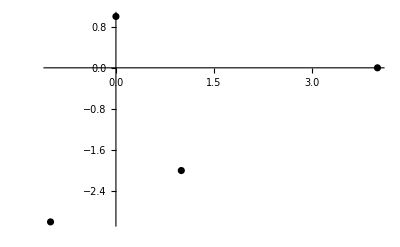

```mathematica
grafico1 = ListPlot[xifi, PlotStyle->Black]
```

```mathematica
fintep[x_] := 1/4*(x-4)*(x+1)*(x-1) + 3/10*(x-4)*x*(x-1) + 1/2*(x-4)*x*(x+1)
```

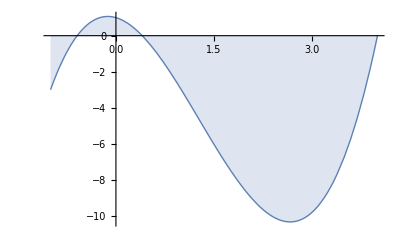

```mathematica
grafico2 = Plot[fintep[x], {x,-1,4}, PlotStyle->Thin, Filling->Axis,FillingStyle->Automatic]
```

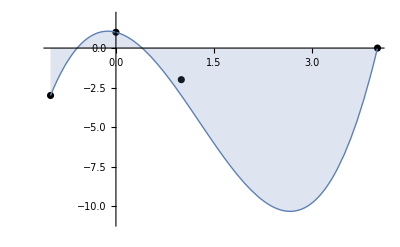

```mathematica
Show[{grafico1, grafico2}, PlotRange -> {{-1,4},{-11,2}}]
```

```mathematica
(*Q1*)
```

```mathematica
xii = {-1, 4,1,5}
fii = {-1,-3,0,-1}
xiifii=Transpose[{xii,fii}]
```

{-1,4,1,5}

{-1,-3,0,-1}

{{-1,-1},{4,-3},{1,0},{5,-1}}

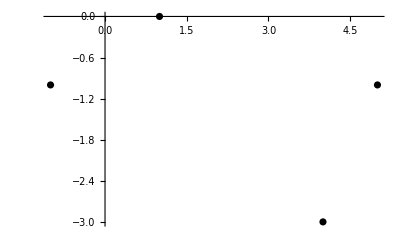

```mathematica
grafico11 = ListPlot[xiifii, PlotStyle->Black]
```

```mathematica
fiintep[x_] := -1-2/5*(x+1) - 3/10*(x-4)*(x+1) + 7/40*(x-4)*(x-1)*(x+1)
```

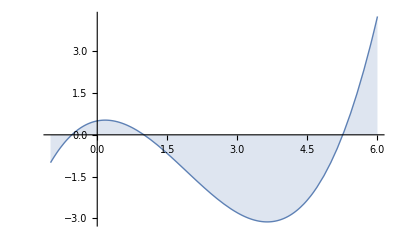

```mathematica
graficos22 = Plot[fiintep[x], {x,-1,6}, PlotStyle->Thin, Filling->Axis,FillingStyle->Automatic]
```

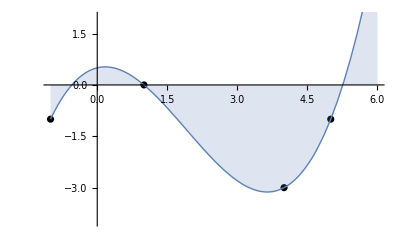

```mathematica
Show[{grafico11, graficos22}, PlotRange -> {{-1,6},{-4,2}}]
```